# Willem Nielsen Work

#### DONE: Very Clean and General Perturbation function, Vis function, Analysis functions, Wfr for Pert function,visualize changes in cells and lifetimes, single pertspec PerturbedCAEvolution function, PerturbedCAEvolution can take multiple coordinates at once, Different genes and phenotypes, Machine learning approach to finding medicine, Adapting under perturbations, testing on different k-values. Maxed out speed with PerturbCAFast

#### TODO: Updating WFR for pert function, k = 5+, try to speed up even more the general perturbation function, Try to get even more robust rules, disease classification for more robust rules, distinguish between antifragile and robust rules

## Functions

### Utility

```mathematica
FrontEndExecute[FrontEnd`AddMenuCommands["DuplicatePreviousOutput",{Delimiter,MenuItem["Delete cell",FrontEnd`KernelExecute[Module[{nb},nb=SelectedNotebook[];
SelectionMove[nb,Previous,Cell];
SelectionMove[nb,Next,Cell];
NotebookDelete[nb];
SelectionMove[nb,Next,Cell]]],MenuKey["k",Modifiers->{"Command"}],System`MenuEvaluator->Automatic]}]]
```

```mathematica
LocationDifferences[arr1_, arr2_, levelspec_:2] := Position[MapThread[{#1, #2} &, {arr1, arr2}, 2], {x_, y_} /; x != y, levelspec]
```

### Perturbation Viz

```mathematica
TrimArray[arr_,{width_,height_}]:=Module[
  {
    w,h,ranges,left,right,lt
  },
  w=If[
    width=!=None,
    ranges=DeleteCases[nonzeroRange /@ arr,{}];
    If[ranges == {}, Return[arr]];
    {left,right}={Min[ranges[[All,1]]],Max[ranges[[All,2]]]};
    #[[Max[1, left-width] ;; Min[Length[arr[[1]]], right+width]]] & /@ arr,
    arr
  ];
  
  h=If[
    height=!=None,
    lt=Length[w]-LengthWhile[Reverse[w],Total[#]==0 &];
    w[[ ;; Min[lt+height,Length[w]]]],
    w
  ]
]
```

```mathematica
ClearAll@PlotCA
```

```mathematica
Options[PlotCA] = {ColorRules -> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, "Trim" -> {1, None}, 
Mesh->False, MeshStyle -> Opacity[0.1]};
PlotCA[ca_, ops:OptionsPattern[]] := With[{allops = Merge[{Options[PlotCA],ops},Last]},
 ArrayPlot[TrimArray[ca, allops["Trim"]], ##]&[FilterRules[Normal[allops], Options[ArrayPlot]]]]

PlotCA[{ruleidx_Integer, k_Integer, r_Integer}, ops:OptionsPattern[]] :=  
With[{allops = Merge[{{"init"->{{1}, 0},"steps"->{100, All}},ops},Last]},
PlotCA[#, Sequence@@Normal[allops]]&[
CellularAutomaton[{ruleidx, k, r}, allops["init"], allops["steps"]]
]]
```

```mathematica
ClearAll@getca
```

```mathematica
getca[ru_, steps_:100, width_:All]:= CellularAutomaton[ru, {{1}, 0}, {steps, width}]
```

```mathematica
ClearAll@PlotDifferences
```

```mathematica
Options[PlotDifferences] = { 
ColorRules -> Join[{0 -> White, -100 -> GrayLevel[.8]}, 
 {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :> Lighter[#2, .7] & @@@ {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
PlotDifferences[arr1_, arr2_, ops:OptionsPattern[]] := 
Module[{locs, vals, rus, highlighted, trimmed, colrules, allops},
	allops=Merge[{Join[Options[PlotCA], Options[PlotDifferences]],ops},Last];
    locs = LocationDifferences[arr1, arr2];
    vals = arr2[[#1, #2]] & @@@ locs;
    rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
    highlighted = ReplacePart[arr1, rus];
    trimmed = TrimArray[highlighted, allops["Trim"]];
    ArrayPlot[trimmed, ##]&[FilterRules[Normal[allops], Options[ArrayPlot]]]
    ]
```

```mathematica
ClearAll@HighlightPerturbations
```

```mathematica
Options[HighlightPerturbations] = {ColorRules->Join[{100->Black},
    #1 -> GrayLevel[0.9] & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 -> #2& @@@ {0->GrayLevel[1],1->RGBColor[1, 0, 0],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
HighlightPerturbations[ca_, ops:OptionsPattern[]]:= Module[{locs, rus, 
highlighted, trimmed, allops},
allops=Merge[{Options[HighlightPerturbations],ops},Last];
locs = Position[ca, perturb[_, _]];
rus = ReplaceAll[#->-ca[[#[[1]], #[[2]], 2]]&/@ locs, 0:>100];
highlighted = ReplacePart[ca,rus];
PlotCA[highlighted, Sequence@@Normal[allops]]
]
```

### Perturbation Function

#### Low level

```mathematica
perturb = Symbol["perturb"];
```

```mathematica
ClearAll@nonzeroRange
```

```mathematica
nonzeroRange[list_]:= SparseArray[list]["NonzeroPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
getbodyidxs[ca_]:= Block[{ranges =DeleteCases[nonzeroRange/@ ca, {}]},
Table[{i, #}&/@ Range@@ranges[[i]], {i, Length[ranges]}]
]
```

```mathematica
ClearAll@getbodyrules
```

```mathematica
getbodyrules[ca_, pertbitfunc_:"Random"]:=
Module[{ranges=DeleteCases[nonzeroRange/@ca,{}]},
Flatten[Table[With[{count=Subtract@@Reverse[ranges[[i]]]+1},
Table[i->{{j},"Enumerate", pertbitfunc},{j,count}]],{i,Length[ranges]}]]]
```

```mathematica
getcoloridxs[ca_]:= 
GatherBy[SparseArray[ca]["NonzeroPositions"], First]
```

```mathematica
getflatcoloridxs[ca_]:= SparseArray[ca]["NonzeroPositions"]
```

```mathematica
ClearAll@getcolorrules
```

```mathematica
getcolorrules[ca_, pertbitfunc_:"Random"]:= Flatten[MapIndexed[#1[[1]]->{#2, "Enumerate", pertbitfunc}&, #]&/@getcoloridxs[ca]]
```

```mathematica
inrange[idxs_, range_ : {1}] := idxs[[Select[range, # >= -Length[idxs] && # <= Length[idxs] &]]]
```

```mathematica
tofunc[bitfuncspec_, k_] := Replace[bitfuncspec, {
   Rule["SetValue", i_Integer] :>  ((perturb[#, i] &) /@ # &),
   Rule["AddValue", i_Integer] :> ((perturb[#, Mod[(# + i), k]] &) /@ # &),
   "Random" :> ((perturb[#, RandomChoice[Complement[Range[0, k - 1], {#}]]] &) /@ # &),
   f_ :> (f[#, k]&)
   }]
```

```mathematica
tofunc2[bitfuncspec_, k_] := Replace[bitfuncspec, {
   Rule["SetValue", i_Integer] :>  (Table[i, Length[#]] &),
   Rule["AddValue", i_Integer] :> ((Mod[(# + i), k] &) /@ # &),
   "Random" :> ((RandomChoice[Complement[Range[0, k - 1], {#}]] &) /@ # &),
   f_ :> (f[#, k]&)
   }]
```

```mathematica
expandrange[range_, n_] := ReplaceAll[
  Replace[range, 
   {(i_Integer) :> If[i >= 1, Range[i], Range[-1, i, -1]],
    List[i_Integer, o__] :> {If[i >= 1, Range[i], Range[-1, i, -1]], o}}],
  {All :> Range[n], {{s_Integer, e_Integer}} :> Range[s, e]}
  ]
```

```mathematica
tofullform[colspec_] :=
 Replace[colspec, {
   {js__Integer} :> {{js}, "Random", "Random"},
   {{js__Integer}, s_String} :> {{js}, s, "Random"},
   {{js__Integer}, s_String, f_} :> {{js}, s, f}}]
```

```mathematica
interpretrule[rule_] := Replace[rule, {
   n_Integer :> {n, 2, 1},
   List[n_Integer, k_Integer] :>  {n, k, 1},
   List[n_Integer, k_Integer, r_?NumberQ] :> {n, k, r},
   List[n_Integer, k_Integer, r_?NumberQ, s_Integer] :> {n, k, r},
   List[n_Integer, List[k_Integer, 1]] :> {n, k, 1},
   List[n_Integer, List[k_Integer, 1], r_?NumberQ] :> {n, k, r}
   }]
```

#### High level

```mathematica
MarkRowPerturbations[row_, colspec_, k_ : 3, r_ : 1] := Module[{coloridxs, range, 
order, bitfunc, sorted, incolorrange, pertbitfunc, vals},
  coloridxs = Replace[nonzeroRange[row], {{} :> {}, g_ :> Range @@ g}];
  {range, order, bitfunc} = tofullform[expandrange[colspec, Length[coloridxs]]];
  sorted = If[order === "Random", RandomSample[coloridxs, UpTo@Length[range]], coloridxs];
  incolorrange = sorted[[Select[range, # >= -Length[sorted] && # <= Length[sorted] &]]];
  pertbitfunc = tofunc[bitfunc, k];
  vals = pertbitfunc[row[[incolorrange]]];
  ReplacePart[row, MapThread[#1 -> #2 &, {incolorrange, vals}]]
  ]
```

```mathematica
MarkPerturbations[{ca_, {n_, k_, r_}}, pertspec_] := 
 {ReplacePart[ca, pertspec[[1]] -> MarkRowPerturbations[ca[[pertspec[[1]]]], pertspec[[2]], k, r]],
  {n, k, r}}
```

```mathematica
ClearAll@MarkPerturbationsByIndex
```

```mathematica
MarkPerturbationsByIndex[{ca_, {n_, k_, r_}}, {idxs_, pertbitfunc_}] := Module[{},
  {ReplacePart[ca, MapThread[#1 -> #2 &, {idxs, pertbitfunc[Flatten[ca[[#1, #2]] & @@@ idxs], k]}]], {n, k, r}}
  ]
```

```mathematica
ClearAll@EvolvePerturbedCA
```

```mathematica
EvolvePerturbedCA[{pca_, rule_}] := Module[{pidxs, pidx, prowidx, pre, prow, evolvedCA},
  pidxs = Position[pca, perturb[_, _], {}];
  If[pidxs == {}, {pca, rule},
   prowidx = pidxs[[1, 1]];
   pre = pca[[;; prowidx - 1]];
   prow = pca[[prowidx]] /. perturb[old_Integer, new_Integer] :> new;
   evolvedCA = Join[pre, CellularAutomaton[rule, prow, Length[pca] - Length[pre] - 1]];
       {evolvedCA, rule}
   ]]
```

```mathematica
ClearAll@PerturbIndexes
```

```mathematica
PerturbIndexes[{ca_, rule_}, idxspec_] := Module[{n, k, r, tolist, idxs, bitfuncspec, byrow},
  {n, k, r} = interpretrule[rule];
  tolist = Replace[idxspec, {{i_Integer, j_Integer} :> {{i, j}}} ];
  {idxs, bitfuncspec} = If[MatchQ[tolist, List[List[_Integer, _Integer] ...]],
   {tolist, "Random"}, {First[tolist], Last[tolist]}];
  byrow = {#, tofunc[bitfuncspec, k]} & /@ GatherBy[SortBy[idxs, #[[1]] &], #[[1]] &];
  Fold[EvolvePerturbedCA[Sow[MarkPerturbationsByIndex[#1, #2]]] &, {ca, {n, k, r}}, byrow]
  ]
```

```mathematica
PerturbIndexesFast[{ca_, rule_}, idxs_:"Random", bitfunc_:"Random"] := Module[{n, k, r,  fidxs, row, vals, newrow, pre},
  {n, k, r} = interpretrule[rule];
  fidxs = If[
    idxs === "Random", RandomSample[getflatcoloridxs[ca], 1], idxs];
  row = ca[[rowidx = fidxs[[1, 1]]]];
  vals  = tofunc2[bitfunc, k][row[[fidxs[[All, 2]]]]];
  newrow = ReplacePart[row, MapThread[#1 -> #2 &, {fidxs[[All, 2]], vals}]];
  pre = ca[[;; rowidx - 1]];
  Join[pre, CellularAutomaton[rule, newrow, Length[ca] - Length[pre] - 1]]
  ]
```

```mathematica
MarkPerturbationsByIndex[{ca_, {n_, k_, r_}}, {idxs_, pertbitfunc_}] := Module[{},
  {ReplacePart[ca, MapThread[#1 -> #2 &, {idxs, pertbitfunc[Flatten[ca[[#1, #2]] & @@@ idxs], k]}]], {n, k, r}}
  ]
```

```mathematica
PerturbCAFast[{ca_, rule_}, rowspec_ -> colspec_, lt_:-1] := Module[{n, k, r, row, rowidx, coloridxs, range, 
   order, bitfunc,topert, pertbitfunc, vals, newrow, pre},
{n, k, r} = interpretrule[rule];
 row = If[rowspec === "Random",
ca[[rowidx = RandomInteger[{1, If[lt == -1, TestCALifeTime[ca] /. -Infinity :> Length[ca], lt]}]]], 
ca[[rowidx = rowspec]]];
coloridxs = If[Length[#] > 0, Range @@ #, #]&@nonzeroRange[row];
{range, order, bitfunc} = tofullform[expandrange[colspec, Length[coloridxs]]];topert = If[order === "Enumerate", coloridxs[[range]], RandomSample[coloridxs, UpTo@Length[range]]];pertbitfunc = tofunc2[bitfunc, k];
    vals = pertbitfunc[row[[topert]]];
newrow = ReplacePart[row, MapThread[#1 -> #2 &, {topert, vals}]];
pre = ca[[;; rowidx - 1]];
     Join[pre, CellularAutomaton[rule, newrow, Length[ca] - Length[pre] - 1]]
    ]
```

```mathematica
ClearAll@PerturbCA
```

```mathematica
PerturbCA[{ca_, rule_}, pertspec_ : "Random"] := Module[{rand, torand, tolist},
  rand = RandomInteger[{1, TestCALifeTime[ca] /. -Infinity :> Length[ca]}];
  torand = Replace[pertspec, {"Random":> rand, Rule["Random", o__]:> rand->o}, {0, 1}];
  tolist = Replace[torand, {i_Integer :> {i -> 1}, r_Rule :> {r}, {i_Integer, j_Integer} :> {{i, j}}}];
  If[MatchQ[tolist, List[Rule[_, _] ..]], 
   Fold[EvolvePerturbedCA[Sow[MarkPerturbations[#1, #2]]] &, {ca, rule}, SortBy[tolist, #[[1]] &]][[1]],
   PerturbIndexes[{ca, rule}, tolist][[1]]]
  ]
```

```mathematica
PerturbCA[{n_Integer, k_Integer, r_?NumberQ}, init_:{{1}, 0}, steps_Integer:100, pertspec_ : "Random"] := Module[{ca, rand, torand, tolist},
  ca = CellularAutomaton[{n, k, r}, init, {steps, All}]; 
  rand = RandomInteger[{1, TestCALifeTime[ca] /. -Infinity :> Length[ca]}];
  torand = Replace[pertspec, {"Random":> rand, Rule["Random", o__]:> rand->o}, {0, 1}];
  tolist = Replace[torand, {i_Integer :> {i -> 1}, ru_Rule :> {ru}, {i_Integer, j_Integer} :> {{i, j}}}];
  If[MatchQ[tolist, List[Rule[_, _] ..]], 
   Fold[EvolvePerturbedCA[Sow[MarkPerturbations[#1, #2]]] &, {ca, {n, k, r}}, SortBy[tolist, #[[1]] &]][[1]],
   PerturbIndexes[{ca, {n, k, r}}, tolist]][[1]]
  ]
```

```mathematica
ClearAll@PerturbedCAEvolution
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_ : 100, pertspec_ : "Random"] := 
  Module[{ca = CellularAutomaton[rule, init, {steps, All}]},
  Replace[pertspec,
   {
    ("Random" | _Integer | _Rule | {_Integer, _Integer} | {_Rule ..} | {{_Integer, _Integer} .. } 
    | {{{_Integer, _Integer} ..  }, _Rule})
     :> EvolvePerturbedCA[Sow[PerturbCA[{ca, rule}, pertspec]]][[1]],
    ({{_Rule ..} ..} | {{{_Integer, _Integer} .. } ..} | {{{{_Integer, _Integer} ..  }, _Rule} ..}
     | {{{{_Integer, _Integer} ..  }, _Rule} ..})
      :> FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, #2]]] &, {ca, rule}, pertspec][[All, 1]],
    {{{{_Integer, _Integer} .. } ..}, r_Rule} :> 
    FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, {#2, r}]]] &, {ca, rule}, First[pertspec]][[All, 1]]
      }
        ]]
```

### Analysis Functions

```mathematica
ClearAll@CountSame
```

```mathematica
CountSame[arr1_, arr2_]:= Block[{sa},sa = SparseArray[arr1-arr2]; Times@@Dimensions[sa] - Length[sa["NonzeroValues"]]]
```

```mathematica
CountDifferences[arr1_,arr2_]:=Length[SparseArray[arr1-arr2]["NonzeroValues"]]
```

```mathematica
TestCALifeTime[ca_]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

```mathematica
PerturbationSensitivity[{ca_, ru_}, pertspec_:("Random"->1), lt_:-1]:= 
With[{clt =If[lt== -1, TestCALifeTime[ca], lt] },
 Abs[
clt - TestCALifeTime[PerturbCAFast[{ca, ru}, pertspec]]]//If[#==Infinity, Max[clt,Length[ca] - clt], #]&
]
```

```mathematica
PerturbationSensitivities[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=PerturbationSensitivity[{ca, ru},#, lt]&/@ getbodyrules[ca, pertbitfunc]
```

```mathematica
ClearAll@PerturbationSensitivities
```

```mathematica
PerturbationSensitivities2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=PerturbationSensitivity[{ca, ru},#, lt]&/@ getcolorrules[ca, pertbitfunc]
```

```mathematica
PerturbationSensitivities2[{initpat, ru}]
```

{91,92,90,92,2,92,92,79,92,92,65,65,73,84,92,92,73,67,73,92,92,92,73,8,92,92,43,92,92,92,92,0,92,92,92,62,92,92,92,92,92,92,92,4,92,92,92,92,92,92,92,55,25,92,92,92,92,59,92,92,92,92,27,92,92,92,92,92,92,92,27,92,92,92,92,92,56,92,92,43,92,92,92,92,92,92,92,5,92,92,92,92,92,92,92,8,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,50,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,38,92,92,92,92,92,92,48,92,34,38,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,1,37,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,41,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,8,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,32,92,92,92,92,92,92,92,92,92,92,92,32,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,21,92,92,92,92,92,92,92,92,92,92,6,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,6,92,92,92,92,92,92,92,92,92,21,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,7,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,12,92,92,4,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,0,92,92,0,92,92,92,92,92,92,0,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,92,92,92,92,6,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,0,92,92,92,92,8,92,92,92,92,0,92,92,92,92,6,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,0,5,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,4,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,0,92,92,0,92,92,0,92,92,92,92,92,92,92,0,92,92,92,92,0,92,92,92,92,92,0,92,0,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,0,92,92,0,0,92,92,92,92,92,92,0,0,92,92,92,92,92,92,0,0,92,0,92,92,92,92,92,92,92,92,9,92,92,92,8,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,0,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,0,0,0,0,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,0,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,0,92,92,0,0,92,92,92,92,92,92,92,92,92,0,92,92,0,0,92,0,0,0,92,92,0,92,92,92,92,92,92,0,0,0,0,92,92,5,92,92,92,92,92,92,0,92,92,92,0,0,92,92,8,92,92,0,92,92,0,92,0,0,92,92,92,92,92,92,92,92,92,92,92,0,0,0,92,92,92,92,92,0,92,92,92,92,92,0,92,0,0,92,92,92,0,92,92,92,0,92,0,0,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,0,0,0,92,92,92,0,7,92,92,92,92,92,0,0,92,92,92,0,92,0,92,92,92,92,92,0,0,92,0,0,0,92,92,0,92,92,92,92,0,92,92,92,92,92,92,92,0,92,0,0,92,0,3,92,92,0,92,92,0,0,0,0,92,92,92,92,92,0,92,0,0,0,92,92,92,92,92,0,92,0,0,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,0,0,92,92,0,0,0,92,0,0,5,92,92,92,92,92,92,92,92,0,92,92,0,7,0,0,92,92,92,7,92,92,92,92,92,92,0,92,0,0,0,92,92,0,0,92,92,7,92,92,92,0,92,0,0,0,0,92,0,0,92,92,7,92,92,92,0,0,0,92,0,92,0,92,0,92,92,92,92,92,92,0,92,0,92,0,0,0,0,0,92,8,3,92,6,92,92,92,92,92,92,92,6,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,6,92,92,92,92,92,92,92,0,92,92,92,7,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,6,92,92,1,92,0,92,2,92,0,92,6,0,0,92,0,0,1}

```mathematica
meanfragility[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, Mean[PerturbationSensitivities[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
meanfragility2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, Mean[PerturbationSensitivities2[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
ClearAll@PerturbationSensitivityPlot
```

```mathematica
PerturbationSensitivityPlot[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= Module[{idxs =Flatten[getbodyidxs[ca], 1], calts},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]]
```

```mathematica
PerturbationSensitivityPlot2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= Module[{idxs =Flatten[getcoloridxs[ca], 1], calts},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities2[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]]
```

### Adapt Therapy

TODO: make arg 11

```mathematica
AdaptTherapy[{initpat_, initru_}, {ca_, currdiff_, mca_, i_}]:= Block[{pca, nca, nmca, newdiff},
nmca = Reap[pca =PerturbCA[{ca, initru}, Floor[11+i]]][[2, 1, 1, 1]];
newdiff = CountDifferences[initpat,pca];
nca = If[newdiff<= currdiff, pca,ca];
{nca, Min[newdiff, currdiff], nmca, i+(1/5)}]
```

### Micro

```mathematica
flipall[bits_, k_]:= ((perturb[#, Complement[Range[0, k - 1], {#}]] &) /@ bits)
```

```mathematica
getperts[tup_, k_]:= Tuples[Replace[ReplacePart[tup, Ceiling[Length[tup] / 2]->Complement[Range[0, k - 1], tup[[{Ceiling[Length[tup] / 2]}]]]], i_Integer:> {i}, 1]]
```

```mathematica
getpertrus[i_, perts_]:= i->#&/@ perts
```

```mathematica
getsubs[{n_, k_, r_}]:= MapThread[#1->#2&, {Tuples[Range[0, k - 1], 1 + 2r],IntegerDigits[n, k, k^(2r+1)]}]
```

```mathematica
getpertedges[k_, r_]:= getpertrus[#, getperts[#, k]]&/@Tuples[Range[0, k - 1],4r+ 1]
```

```mathematica
getruparts[arr1_->arr2_, r_:1]:= Transpose[Partition[#, 2r+1, 1]&/@ {arr1, arr2}]
```

```mathematica
pertdiffs[{n_, k_, r_}]:= Block[{ruparts, stepped},
 ruparts =Map[getruparts[#, r]&, getpertedges[ k, r], {2}];
stepped = Replace[ruparts, l_List:> Replace[l, getsubs[{n, k, r}], {4}]];
Map[Abs[#[[1]] - #[[2]]]&, stepped, {3}]]
```

```mathematica
totalpertdiffs[ru_]:= Total[pertdiffs[ru], 3]
```

```mathematica
TestLifetime[rule_,init_List:{1},
max_Integer:100(*,infinity_:Infinity*)]:=With[
{array=CellularAutomaton[rule,{init,0},{max,All}]},If[#==0,-Infinity(*-infinity*),max-#+1]&[
LengthWhile[Reverse[array],Total[#]==0&]
]
]
```

```mathematica
RuleTuples[k_,r_]:=RuleTuples[k,r]=Tuples[
Reverse[Range[0,k-1]],2r+1]
```

```mathematica
RuleMask[{ru_,k_,r_},lt_]:=Module[
{data,mask,canonical},
data=Union[Catenate[Map[Partition[#,2r+1,1]&,
CellularAutomaton[{ru,k,r},
CenterArray[1,2 r*(lt+4)+1],lt+2]]]];
mask=Lookup[Association[Thread[data->1]],RuleTuples[k,r],0]
(*canonical=IntegerDigits[ru,k,Length[mask]];{
FromDigits[canonical*mask,k],
FromDigits[mask,2]
}*)
]
```

```mathematica
getruleloc[bits_, k_, r_] := FirstPosition[RuleTuples[k, r], bits][[1]]
```

```mathematica
plotrule[rule_, ops:OptionsPattern[{"Trim"->{None, None}, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= Module[{digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
PlotCA[{digits}, "Trim"->OptionValue["Trim"],ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
plotmaskedrule[rule_, ops:OptionsPattern[{"Overlap"->False,"Trim"->{None, None}, ColorRules->withmask,Mesh->True, MeshStyle->Gray, ArrayPlot}]]:= Module[{n, k, r, mult, mask, masked,digits},
{n, k, r} =interpretrule[rule];
digits = IntegerDigits[n, k, k^(2r+1)];
mult = If[OptionValue["Overlap"], -1, 100];
mask = RuleMask[rule, TestLifetime[rule, 200]]*mult;
masked = (mask/. 0:> 1) * ReplaceAll[digits, 0:> 100];
PlotCA[If[OptionValue["Overlap"], {masked}, {digits, mask}], "Trim"->OptionValue["Trim"],ColorRules->OptionValue[ColorRules],
   Mesh -> OptionValue[Mesh], MeshStyle -> OptionValue[MeshStyle], ImageSize -> OptionValue[ImageSize]]
]
```

```mathematica
getgenelocs[{pca_, ru_}]:= Module[{n, k, r, pidxs, windows, oldwindows, newwindows, oldrulesets, newrulesets, genepairs, locs}, 
{n, k, r} = interpretrule[ru];
pidxs = Position[pca, perturb[_,_], {}];
windows = pca[[#[[1]], #[[2]]- 2r;;#[[2]]+ 2r]]&/@ pidxs;
oldwindows = # /. perturb[old_Integer, new_Integer]:> old&/@windows;
newwindows = # /. perturb[old_Integer, new_Integer]:> new&/@windows;
oldrulesets = Partition[#, 2r+1, 1]&/@ oldwindows;
newrulesets = Partition[#, 2r+1, 1]&/@ newwindows;
genepairs = MapThread[{#1, #2}&, {oldrulesets, newrulesets}, 2];
locs = Map[getruleloc[#, k, r]&, genepairs, {3}] - 1/2
]
```

```mathematica
overlaplightrules = Join[{-100 -> GrayLevel[.8]}, 
   #1 :> Lighter[#2, .7] & @@@{100->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :>#2 & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

If active lighter, if white active gray

```mathematica
overlapdarkrules =  Join[{100 -> GrayLevel[.5]}, 
   -#1 :> Lighter[#2, .7] & @@@{100->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    #1 :>#2 & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}];
```

```mathematica
withmask ={0->GrayLevel[1], 1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 100->GrayLevel[0.2]};
```

```mathematica
getmidx[x1_, x2_]:= (x1 - x2)/ 2+x2
```

```mathematica
ClearAll@getcurves
```

```mathematica
getcurves[locs_, y_:2]:= Module[{withmid, pts, curves, witharrows},
withmid = Map[{#[[1]], getmidx[#[[1]], #[[2]]], #[[2]]}&, locs, {2}];
pts = Map[{{#[[1]], y}, {#[[2]],y+2}, {#[[3]], y}} &, withmid, {2}];
curves = Map[BezierCurve, pts, {2} ];
witharrows = Arrow/@ Flatten[curves];
Graphics[{Arrowheads[0.025],GrayLevel[0.4], witharrows}]
]
```

```mathematica
ClearAll@PerturbedRulePlot
```

```mathematica
PerturbedRulePlot[{pca_, ru_},OptionsPattern[{"Mask"->False}]]:= 
If[OptionValue["Mask"], Show[plotmaskedrule[ru],getcurves[getgenelocs[{pca, ru} ], 2]], 
Show[plotrule[ru],getcurves[getgenelocs[{pca, ru}], 1]]]
```

## Running Code

### Init

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
```

```mathematica
rrus ={#, 3, 1}&/@ {4201857261303,4201857263490,4201857263409,4201856731968};
```

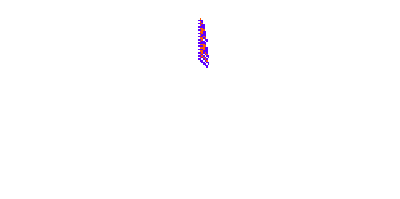
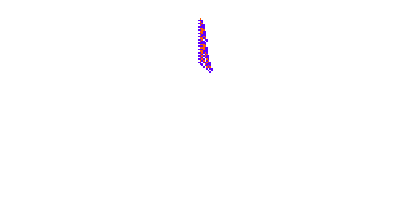
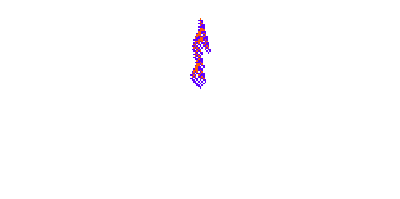
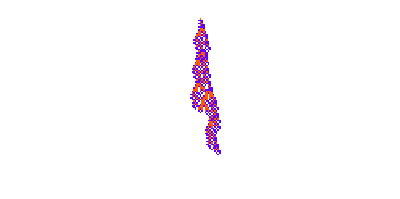

```mathematica
PlotCA/@ rrus
```

### Adaptive Therapy

#### Sickness

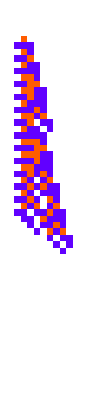
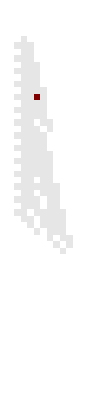
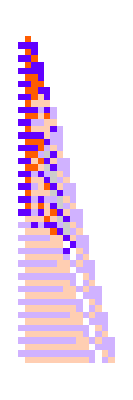
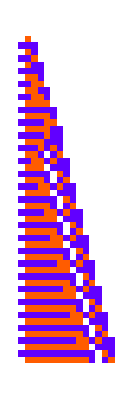
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,325}

```mathematica
SeedRandom[4286];
pat = CellularAutomaton[rrus[[2]], {{1}, 0}, {50, All}];
marked = Reap[sick = PerturbCA[{pat, rrus[[2]]}, 10->{{4}, "Enumerate", "SetValue"->1}]][[2, 1, 1, 1]];
{PlotCA[pat],HighlightPerturbations[marked], PlotDifferences[pat, sick], PlotCA[sick], currdiff = CountDifferences[pat, sick]}
```

#### Adaptive Therapy

```mathematica
RandomSeed[1125];
evo = NestList[AdaptTherapy[{pat, rrus[[2]]}, #]& , {sick, currdiff, sick, 0}, 200];
```

```mathematica
unique = DeleteDuplicatesBy[evo, #[[2]]&];
```

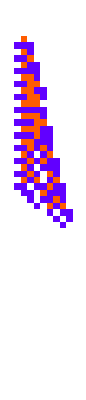
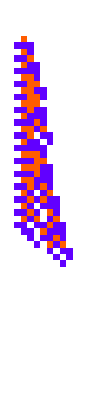
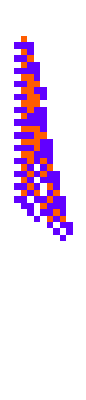
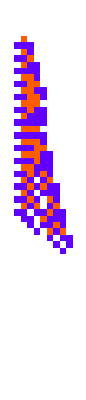
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@unique[[All, 1]]
```

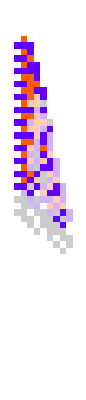
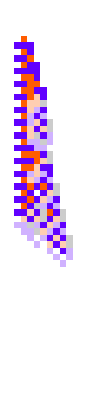
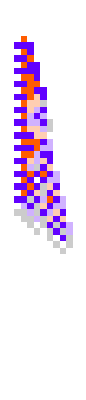
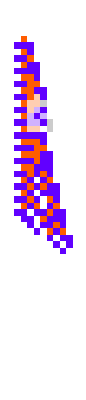
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences[pat, #]&/@ unique[[All, 1]]
```

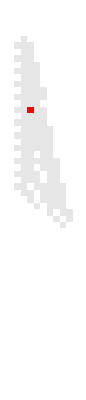
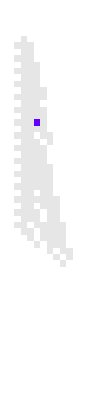
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightPerturbations/@ unique[[All, 3]]
```

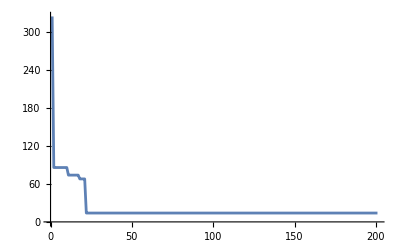

```mathematica
ListLinePlot[evo[[All, 2]]]
```

```mathematica
evos = Table[ NestList[AdaptTherapy[{pat, rrus[[2]]}, #]& , {sick, currdiff, sick, 0}, 100], 10]
```

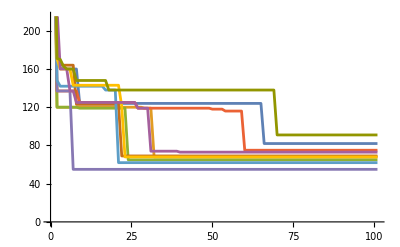

```mathematica
ListLinePlot[evos[[All, All, 2]]]
```

#### Other Rules For Adaptive Therapy

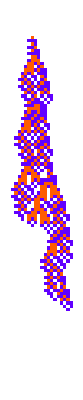
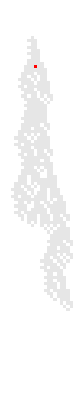
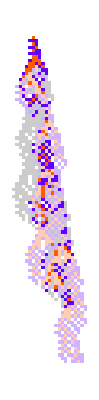
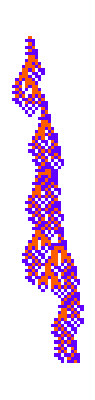
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,786}

```mathematica
pat2 = CellularAutomaton[rrus[[4]], {{1}, 0}, {100, All}];
marked2 = Reap[sick2 = PerturbCA[{pat2, rrus[[4]]}, 10->{{4}, "Enumerate", "SetValue"->1}]][[2, 1, 1, 1]];
{PlotCA[pat2],HighlightPerturbations[marked2], PlotDifferences[pat2, sick2], PlotCA[sick2], currdiff2 = CountDifferences[pat2, sick2]}
```

```mathematica
SeedRandom[4444];
evo2 = NestList[AdaptTherapy[{pat2, rrus[[4]]}, #]& , {sick2, currdiff2, sick2, 0}, 200];
```

```mathematica
unique2 = DeleteDuplicatesBy[evo2, #[[2]]&];
```

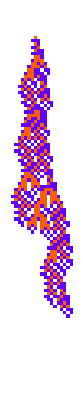
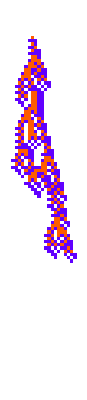
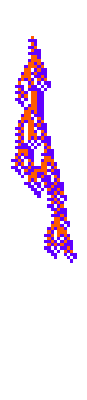
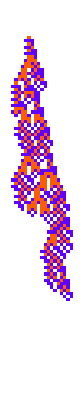
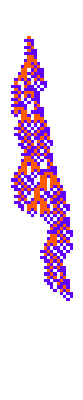
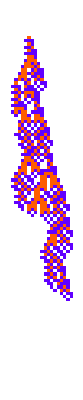
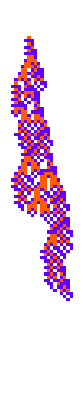
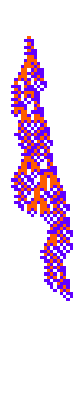
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@unique2[[All, 1]]
```

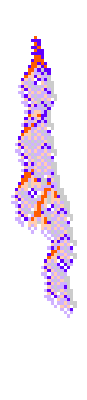
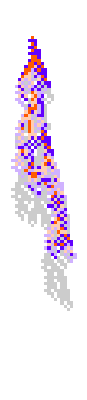
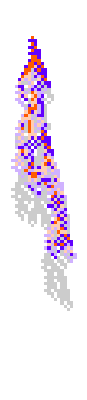
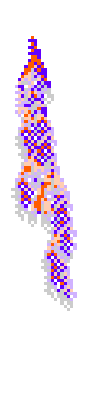
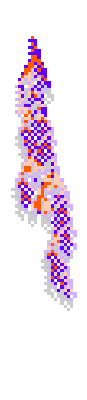
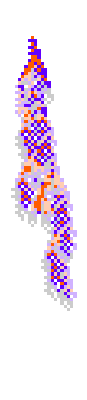
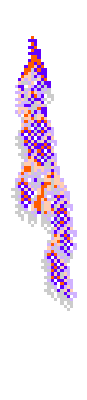
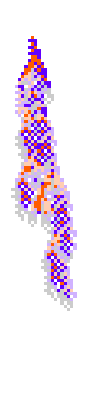
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences[pat2, #]&/@ unique2[[All, 1]]
```

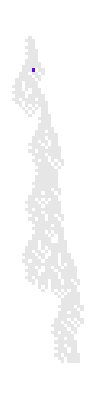
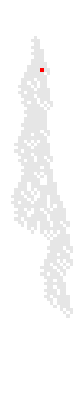
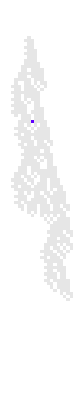
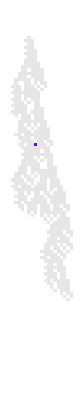
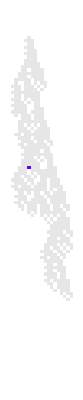
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightPerturbations/@ unique2[[All, 3]]
```

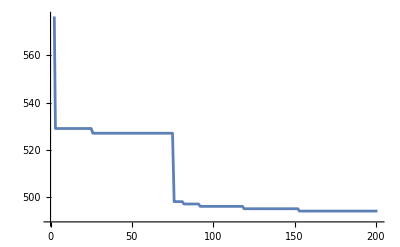

```mathematica
ListLinePlot[evo2[[All, 2]]]
```

```mathematica
evos2 = Table[ NestList[AdaptTherapy[{pat2, rrus[[4]]}, #]& , {sick2, currdiff2, sick2, 0}, 200], 10]
```

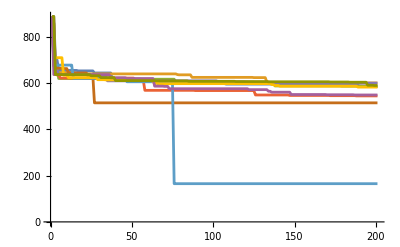

```mathematica
ListLinePlot[evos2[[All, All, 2]], PlotRange->All]
```

### Mean/Min Adaptive Evolution Under Perturbations

It works, evolution under perturbations seems to favor “slower growers” or skinnier patterns that don’t collide. The minimum lifetime after the perturbations seems to work better than mean. Evolution seems to move a bit slower.

#### Min k = 4

```mathematica
randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
```

```mathematica
evo42=Module[{ru, ca, lt, pcas, fitness},
SeedRandom[426778];
NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},5000]
];
```

```mathematica
unique42 = DeleteDuplicatesBy[evo42[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

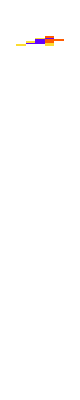
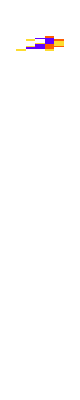
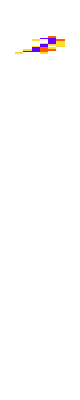
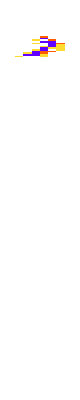
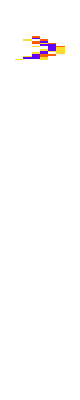
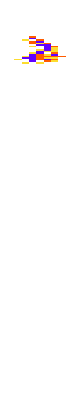
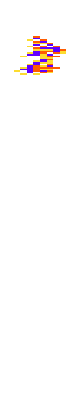
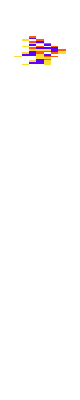
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[#,"steps"->200, "init"->{{1}, 0}]&/@ unique42
```

Sample Perturbations to the final rule

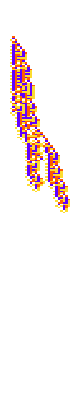
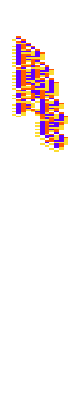
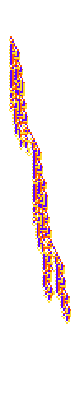
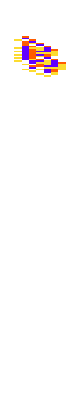
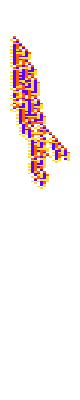
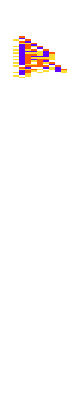
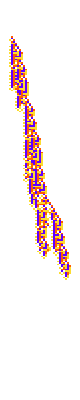
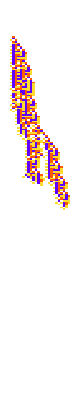
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evo42[[-1, 1]], {{1}, 0}, {200, All}], evo42[[-1, 1]]}], 10]
```

#### Mean k = 4

```mathematica
evo4=Module[{ru, ca, lt, pcas, fitness},
SeedRandom[426778];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {100, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCA[{ca, ru}, "Random"->Ceiling[lt /2]], 1];
fitness = Mean[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},5000]
];
```

```mathematica
unique4 = DeleteDuplicatesBy[evo4[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

```mathematica
PlotCA[#,"steps"->100, "init"->{{1}, 0}]&/@ unique4
```

{-Graphics-}

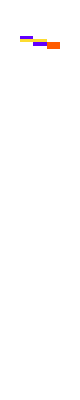
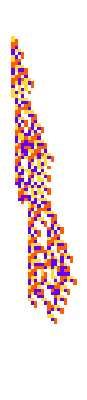
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evo4[[-1, 1]], {{1}, 0}, {100, All}], evo4[[-1, 1]]}], 10]
```

#### Regular k = 4 for comparison

```mathematica
evoreg4 = Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]]
];
```

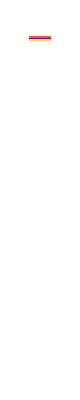
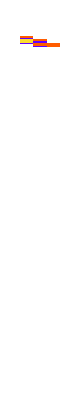
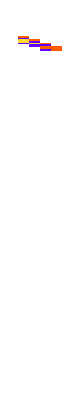
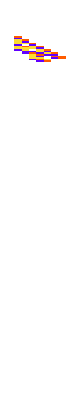
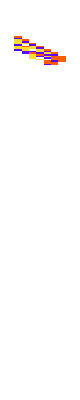
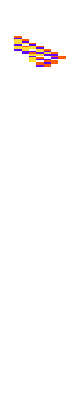
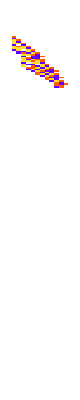
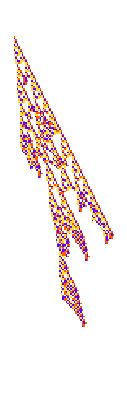
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[#, "steps"->200, "init"->{{1}, 0}]&/@ evoreg4[[All, 1]]
```

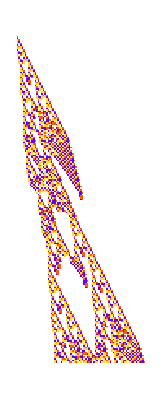
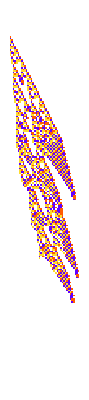
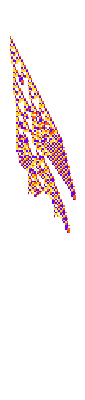
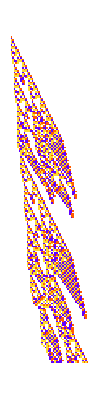
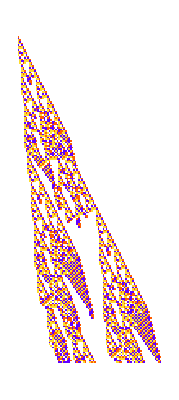
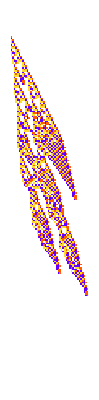
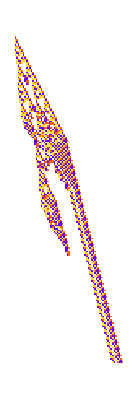
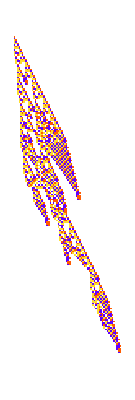

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evoreg4[[-1, 1]], {{1}, 0}, {200, All}], evoreg4[[-1, 1]]}], 10]
```

#### Distribution Chart Comparison Perturbed Vs. Regular Evolution k = 4

```mathematica
p4 = unique42;
r4 = evoreg4[[All, 1]];
```

```mathematica
sickp4s = Table[Table[PerturbCA[{CellularAutomaton[p4[[i]], {{1}, 0}, {200, All}], p4[[i]]}], 100], {i,1, Length[p4]}];
sickr4s = Table[Table[PerturbCA[{CellularAutomaton[r4[[i]], {{1}, 0}, {200, All}], r4[[i]]}], 100], {i,1, Length[r4]}];
p4lts = Map[TestCALifeTime,sickp4s, {2}];
r4lts =  Map[TestCALifeTime,sickr4s, {2}];
```

Evolved Under Perturbation on the Left and Regular on the Right

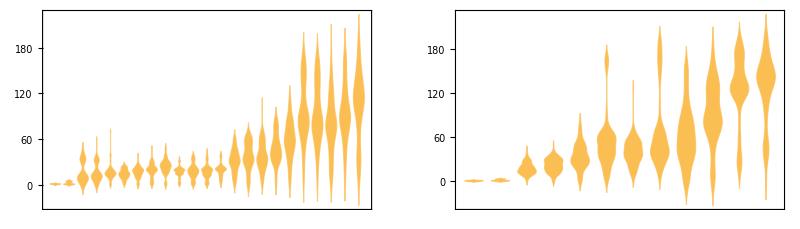

```mathematica
GraphicsRow[{DistributionChart[p4lts], DistributionChart[r4lts]}]
```

With infinities going to 0

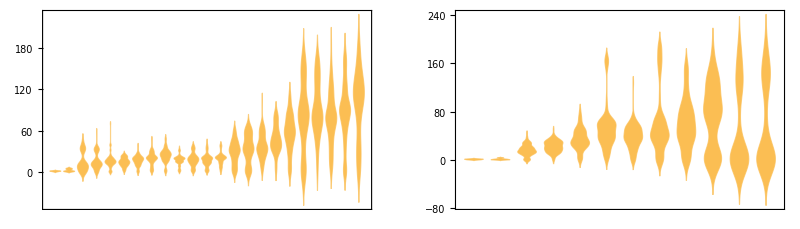

```mathematica
GraphicsRow[{DistributionChart[p4lts/. -Infinity:> 0],DistributionChart[r4lts/. -Infinity:> 0]}]
```

#### Min k = 3

```mathematica
evo32=Module[{ru, ca, lt, pcas, fitness},
SeedRandom[444999];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {100, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCA[{ca, ru}, "Random"->Ceiling[lt /2]], 1];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,3,1},0},4000]
];
```

```mathematica
unique32 = DeleteDuplicatesBy[evo32[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

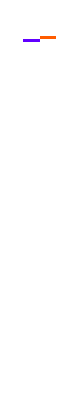
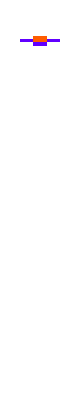
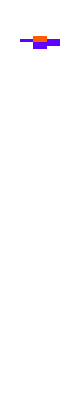
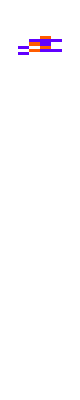
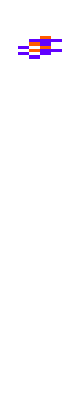
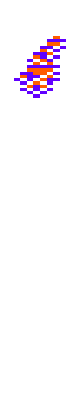
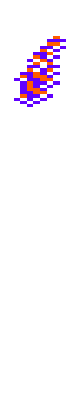
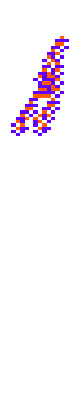
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[#,"steps"->100, "init"->{{1}, 0}]&/@ unique32
```

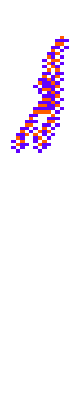
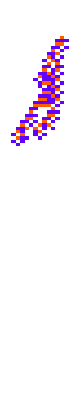
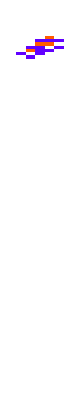
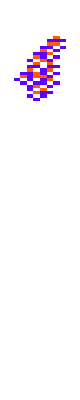
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evo32[[-1, 1]], {{1}, 0}, {100, All}], evo32[[-1, 1]]}], 10]
```

#### Mean k =3

```mathematica
evo3=Module[{ru, ca, lt, pcas, fitness},
SeedRandom[426778];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {100, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCA[{ca, ru}, "Random"->Ceiling[lt /2]], 1];
fitness = Mean[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,3,1},0},4000]
];
```

```mathematica
unique3 = DeleteDuplicatesBy[evo3[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

```mathematica
PlotCA[#,"steps"->100, "init"->{{1}, 0}]&/@ unique3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evo3[[-1, 1]], {{1}, 0}, {100, All}], evo3[[-1, 1]]}], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Regular for comparison

```mathematica
evoreg = Module[
{deep=4000,cut=200,ru,life,evo,data},
SeedRandom[111333];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]]
];
```

```mathematica
PlotCA[#, "steps"->100, "init"->{{1}, 0}]&/@ evoreg[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evoreg[[-1, 1]], {{1}, 0}, {100, All}], evoreg[[-1, 1]]}], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Distribution Chart Comparison Perturbed Vs. Regular Evolution k = 3

```mathematica
p3 = unique32;
r3 = evoreg[[All, 1]];
```

```mathematica
sickp3s = Table[Table[PerturbCA[{CellularAutomaton[p3[[i]], {{1}, 0}, {200, All}], p3[[i]]}], 100], {i,1, Length[p3]}];
sickr3s = Table[Table[PerturbCA[{CellularAutomaton[r3[[i]], {{1}, 0}, {200, All}], r3[[i]]}], 100], {i,1, Length[r3]}];
p3lts = Map[TestCALifeTime,sickp3s, {2}];
r3lts =  Map[TestCALifeTime,sickr3s, {2}];
```

Evolved Under Perturbation on the Left and Regular on the Right. Rules go in their evolved order

```mathematica
GraphicsRow[{DistributionChart[p3lts, PlotRange->{-20, 150}], DistributionChart[r3lts, PlotRange->{-20, 150}]}]
```

-Graphics-

With infinities going to 0

```mathematica
GraphicsRow[{DistributionChart[p3lts/. -Infinity:> 0, PlotRange->{-20, 150}],DistributionChart[r3lts/. -Infinity:> 0, PlotRange->{-20, 150}]}]
```

-Graphics-

### What exactly is going on when a perturbation happens?

Here we’re looking at all possible single perturbations for k = 3 and r = 1. For r = 1 cases, the effected span is 5 cells wide.

```mathematica
UndirectedGraph[Catenate[getpertedges[3, 1]],EdgeStyle->Opacity[.4],VertexSize->0,VertexLabels->{x_:>Placed[ArrayPlot[{x},
Mesh->True,ImageSize->40, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}],Center]}, GraphLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

#### Total robustness of ruleset metric

The edges correspond to a perturbation, and if the connected vertices produce the same output, that means the ruleset is robust to that specific perturbation. We can measure the total differences of all possible perturbations on a given ruleset. Running that metric across an evolution we get:

```mathematica
BarChart[totalpertdiffs/@evoreg[[All, 1]]]
```

-Graphics-

For k = 4 it’s a similar story

-Graphics-

So with rulesets that aren’t very simple like the all white case, we get an increase in the fragility of the ruleset. Here is a n = 500 random sample of the k = 3 ruleset

```mathematica
ListLinePlot[Table[totalpertdiffs[{RandomInteger[{1, 7625597484987}], 3, 1}], 500]]
```

-Graphics-

#### Perturbation Rule Plot

With each of those cell spans, there are three overlapping rules (in the r = 1 case) that are changed. If all three of those rules are the same then the rule will be robust to that perturbation. We can visualize this effect like so:

```mathematica
PerturbedRulePlot[MarkPerturbations[{CellularAutomaton[r3[[10]], {{1}, 0}, {10, All}], r3[[10]]}, 2->1]]
```

-Graphics-

Looking at different perturbations:

```mathematica
SeedRandom[555777];
Column[Table[PerturbedRulePlot[MarkPerturbations[{CellularAutomaton[r3[[10]], {{1}, 0}, {10, All}], r3[[10]]}, 2->1]], 10]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

So as we can this is pretty rare. But, one can imagine having a frequent perturbation and selecting mutations that reduce it’s effect. This would involve changing unused rules, to match the perturbed ones. To see if this is possible we can look at whether a rule is used as well as it’s color like so:

```mathematica
PerturbedRulePlot[MarkPerturbations[{CellularAutomaton[r3[[3]], {{1}, 0}, {10, All}], r3[[3]]}, 2->1], "Mask"->True]
```

-Graphics-

And indeed in this case, we aren’t using that many rules so it would be possible to instantly heal by changing the three new rules to match the old ones. But this is for a very small CA:

```mathematica
PlotCA[r3[[3]], "Trim"->{2, 10}, ImageSize->Small]
```

-Graphics-

For more complex automata and k = 3, instantly healing won’t be possible without having some other “sickness” develop. Here we show the effect of a perturbation across an evolution:

```mathematica
SeedRandom[555777];
Column[Table[PerturbedRulePlot[MarkPerturbations[{CellularAutomaton[r3[[i]], {{1}, 0}, {10, All}], r3[[i]]}, i-1->1], "Mask"->True], {i, 5, Length[r3]}]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### Loading rules

```mathematica
r3 ={{243,3,1},{1753938218655,3,1},{5989249952505,3,1},{3401069339025,3,1},{1046114442267,3,1},{1046109659055,3,1},{6131026665339,3,1},{7019083117725,3,1},{7020240596223,3,1},{6171790079607,3,1},{6178725384657,3,1},{6178809883776,3,1},{6173014224426,3,1},{5984727748674,3,1}};
```

```mathematica
p3 = {{0,3,1},{39516894258,3,1},{5275775000895,3,1},{5275803698709,3,1},{5946201042513,3,1},{6138184930449,3,1},{4307711225406,3,1},{4401849503166,3,1},{4401852691812,3,1},{4433233751421,3,1}};
```

```mathematica
p4 = {{0,4,1},{158645367558720280680054855075477641276,4,1},{158645367558720280680054573875377789500,4,1},{158645367558720280666219529082954635832,4,1},{159309981556612740963854674047917414968,4,1},{196444670383646442864375227283730340400,4,1},{196611472603323895551390670641720465968,4,1},{108877881631671750362806180319376972336,4,1},{108877881631671750362806180319376980528,4,1},{108545574632725521394580228554306894384,4,1},{151163947251293207867720325390307703344,4,1},{151163947251293206613341731676593076784,4,1},{151163947251525320370706614577692949040,4,1},{156483470614708570202183427193640073776,4,1},{156317317115235458079253692745927653936,4,1},{156312043682548808448516551617146288688,4,1},{158970499674118640194324165737706977840,4,1},{158982182347002103713631006353816844848,4,1},{158982182347002103713631006645874620976,4,1},{158982182347002103713631006370996714032,4,1},{158982182347002103566057053781253192240,4,1},{158982020087725274352693660004219648560,4,1},{158982020087725274942989470362925300272,4,1}};
```

```mathematica
r4 = {{1180591620717411303424,4,1},{71605777279541226340392202479209756160,4,1},{131665181873339428235310154952426592768,4,1},{256623566927192160560278656322908658176,4,1},{256623566927192160559125734818570246656,4,1},{256623566927192160559139245617452358144,4,1},{256623566927192160559175274414471322112,4,1},{257620650182088474988135449789733214720,4,1},{2408874991385231853442191159898348032,4,1},{2408874991385231853442191159898352128,4,1}};
```

```mathematica
PlotCA/@ p4
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### k = 4 antifragile agnostic

```mathematica
fitsmemo = {};
evo43=Module[{ru, ca, lt, pcas, fits, fitness, fitdiff},
SeedRandom[444997];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCAFast[{ca, ru}, "Random"->1, lt], Ceiling[lt/10]];
fits = Join[TestCALifeTime/@ pcas];
fitness = Mean[If[# == {}, {0}, #]&[Select[fits, #<= lt&]]];
AppendTo[fitsmemo, fits];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},4000]
];
```

```mathematica
unique43 = DeleteDuplicatesBy[evo43[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

```mathematica
PlotCA[#,"steps"->200, "init"->{{1}, 0}]&/@ unique43
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Sample Perturbations to the final rule

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evo43[[-1, 1]], {{1}, 0}, {200, All}], evo43[[-1, 1]]}, "Random"->1], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[evo43[[All, 2]]]
```

-Graphics-

```mathematica
N@meanfragility[{getca[unique43[[-1]]],unique43[[-1]]}]
```

64.9194

### k = 4 selecting only rules with a minimum variation in lifetime after perturbation

```mathematica
evo44=Module[{ru, ca, lt, pcas, fits, fitness, fitdiff},
SeedRandom[444997];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCAFast[{ca, ru}, "Random"->Ceiling[lt/20], lt], Ceiling[lt/10]];
fits = TestCALifeTime/@ pcas;
fitdiff = Abs[lt - Mean[ fits]];
If[lt>=Last[#]&& fitdiff <= 2,{ru,lt},#]
]]&,{{0,4,1},0},4000]
];
```

```mathematica
unique44 = DeleteDuplicatesBy[evo44[[All, 1]], {{"[◼]", "TestLifetime"}}];
```

```mathematica
PlotCA[#,"steps"->200, "init"->{{1}, 0}]&/@ unique44
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Sample Perturbations to the final rule

```mathematica
PlotCA/@ Table[PerturbCA[{CellularAutomaton[evo44[[-1, 1]], {{1}, 0}, {200, All}], evo44[[-1, 1]]}, "Random"->1], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
N@meanfragility[{getca[unique44[[-1]]],unique44[[-1]]}]
```

61.3374

```mathematica
GraphicsRow[SeedRandom[234243];
HighlightPerturbations/@ Table[Reap[PerturbCA[{CellularAutomaton[evo44[[-1, 1]], {{1}, 0}, {200, All}], evo44[[-1, 1]]}, "Random"->1]][[2, 1, 1, 1]], 10]]
```

-Graphics-

```mathematica
PerturbationSensitivityPlot[{getca[evo44[[-1, 1]], 200], evo44[[-1, 1]]}]
```

-Graphics-

```mathematica
meanfragility[{getca[evo44[[-1, 1]], 200], evo44[[-1, 1]]}] // N
```

34.5062

```mathematica
ListLinePlot[evo44[[All, 2]]]
```

-Graphics-

### Evolving From Regular to Robust

```mathematica
PlotCA/@ r3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
rca =CellularAutomaton[r3[[-1]], {{1}, 0}, {100, All}];
marked = Reap[pca = PerturbCA[{CellularAutomaton[r3[[-1]], {{1}, 0}, {100, All}], r3[[-1]]}, "Random"->{{-1}, "Enumerate"}]][[2, 1,1, 1]];
{PlotCA[rca, ImageSize->Medium], HighlightPerturbations[marked], PlotDifferences[rca, pca], PlotCA[pca, ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
evo34 = Module[
{deep=4000,cut=200,initlife = {{"[◼]", "TestLifetime"}}[r3[[-1]]],mca = marked,pca, ru, life,diff, evo,data},
SeedRandom[426770];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
pca = EvolvePerturbedCA[{mca, ru}][[1]],
life=TestCALifeTime[pca],
diff = Abs[initlife  - life];
If[diff<=Last[#],{ru,diff},#]
]&,{r3[[-1]],Infinity},deep]
];
```

```mathematica
GraphicsRow[PlotCA[EvolvePerturbedCA[{marked, #[[1, 1]]}][[1]]]&/@SplitBy[evo34,Last]]
```

-Graphics-

```mathematica
SplitBy[evo34,Last][[-1, 1]]
```

{{5963807088438,3,1},1}

```mathematica
PerturbationSensitivityPlot[{rca, r3[[-1]]}]
```

-Graphics-

```mathematica
PerturbationSensitivityPlot[EvolvePerturbedCA[{marked, SplitBy[evo34,Last][[-1, 1, 1]]}]]
```

-Graphics-

### Lowering Mean Fragility

```mathematica
evo35 = Module[
{deep=1000,cut=200,initlife = {{"[◼]", "TestLifetime"}}[r3[[-2]]],lt, ca ,mf, ru, life, evo,data},
SeedRandom[426750];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[ru];lt = TestCALifeTime[ca];
If[lt != initlife, #,
mf = meanfragility[{ca, ru}];
If[mf<=Last[#],{ru,mf},#]
]]&,{r3[[-2]],Infinity},deep]
];
```

```mathematica
PlotCA[#[[1, 1]]]&/@SplitBy[evo35,Last]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "RulesMutationPlot"}}[SplitBy[evo35,Last][[All, 1,1]]]
```

-Graphics-

```mathematica
plotmaskedrule[SplitBy[evo35,Last][[-1, 1, 1]]]
```

-Graphics-

```mathematica
N@SplitBy[evo35,Last][[All, 1, 2]]
```

{∞,27.2927,24.1902,19.6634,15.2537,15.2049,14.5024,13.4098,12.9756,12.7512,12.7122}

```mathematica
PerturbationSensitivityPlot[{getca[#[[1, 1]]], #[[1, 1]]}]&/@SplitBy[evo35,Last]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[Table[PerturbationSensitivity[{getca[#], #}, "Random"->1], 1000]&@r3[[-2]]]
```

-Graphics-

```mathematica
Histogram[Table[PerturbationSensitivity[{getca[#], #}, "Random"->1], 1000]&@SplitBy[evo35,Last][[-1, 1, 1]]]
```

-Graphics-

```mathematica
lp = SplitBy[evo35,Last][[-1, 1, 1]];
```

```mathematica
PlotCA/@Table[PerturbCAFast[{getca[#], #}, "Random"->1], 10]&@SplitBy[evo35,Last][[-1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbCA[rca = {getca[r3[[-1]]], r3[[-1]]}, "Random"->{{-1}, "Enumerate"}]
```

```mathematica
marked = Reap[pca = PerturbCA[{rca = getca[r3[[-2]]], r3[[-2]]},20->{{1}, "Enumerate", "SetValue"->1}]][[2, 1,1, 1]];
{PlotCA[rca, ImageSize->Large],HighlightPerturbations[marked, ImageSize->Large], PlotDifferences[rca, pca, ImageSize->Large],PlotCA[pca, ImageSize->Large]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
new = {{"[◼]", "RandomRuleMutation"}}[r3[[-2]]];
```

```mathematica
{{"[◼]", "RulesMutationPlot"}}[{r3[[-2]], new}]
```

-Graphics-

```mathematica
plotmaskedrule[r3[[-2]]]
```

-Graphics-

```mathematica
{{"[◼]", "RulesMutationPlot"}} [{r3[[-2]], {{"[◼]", "RandomRuleMutation"}}[r3[[-2]]]}]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[new], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[r3[[-2]]], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

-Graphics-

```mathematica
N@{meanfragility[{getca[r3[[-2]]], r3[[-2]]}], meanfragility[{getca[new], new}]}
```

{26.6634,23.9024}

```mathematica
{PerturbationSensitivityPlot[{getca[r3[[-2]]], r3[[-2]]}], PerturbationSensitivityPlot[{getca[new], new}]}
```

{-Graphics-,-Graphics-}

```mathematica
marked = Reap[pca = PerturbCA[{rca = getca[new],new},20->{{1}, "Enumerate"}]][[2, 1,1, 1]];
{PlotCA[rca, ImageSize->Large],HighlightPerturbations[marked, ImageSize->Large], PlotDifferences[rca, pca, ImageSize->Large],PlotCA[pca, ImageSize->Large]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
evo35 = Module[
{deep=1000,cut=200,initlife = {{"[◼]", "TestLifetime"}}[r3[[-2]]],lt, ca ,mf, ru, life, evo,data},
SeedRandom[426750];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = getca[ru];lt = TestCALifeTime[ca];
If[lt != initlife, #,
mf = meanfragility[{ca, ru}];
If[mf<=Last[#],{ru,mf},#]
]]&,{r3[[-2]],Infinity},deep]
];
```

### Genome growth rate

```mathematica
4^(2+1)
```

64

```mathematica
k4allrobust = ;
k4allreg = ;
```

```mathematica
digs = IntegerDigits[#[[1]], #[[2]], 64]&/@ #&/@ {k4s[[All, 1]],k4rs[[All, 1]]};
```

```mathematica
Count[#, 0]&/@ digs[[1]] // Mean // N
```

21.1

```mathematica
Count[#, 0]&/@ digs[[2]] // Mean // N
```

18.3333

```mathematica
Column[plotrule[#, ImageSize->Medium]&/@ k4s[[All, 1]]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### Perturbation Sensitivity Plots

#### Functions

```mathematica
PerturbationSensitivity[{ca_, ru_}, pertspec_:("Random"->1), lt_:-1]:= 
With[{clt =If[lt== -1, TestCALifeTime[ca], lt] },
 Abs[
clt - TestCALifeTime[PerturbCAFast[{ca, ru}, pertspec]]]//If[#==Infinity, Max[clt,Length[ca] - clt], #]&
]
```

```mathematica
PerturbationSensitivities[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=PerturbationSensitivity[{ca, ru},#, lt]&/@ getbodyrules[ca, pertbitfunc]
```

```mathematica
ClearAll@PerturbationSensitivities
```

```mathematica
PerturbationSensitivities2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:=PerturbationSensitivity[{ca, ru},#, lt]&/@ getcolorrules[ca, pertbitfunc]
```

```mathematica
PerturbationSensitivities2[{initpat, ru}]
```

{91,92,90,92,2,92,92,79,92,92,65,65,73,84,92,92,73,67,73,92,92,92,73,8,92,92,43,92,92,92,92,0,92,92,92,62,92,92,92,92,92,92,92,4,92,92,92,92,92,92,92,55,25,92,92,92,92,59,92,92,92,92,27,92,92,92,92,92,92,92,27,92,92,92,92,92,56,92,92,43,92,92,92,92,92,92,92,5,92,92,92,92,92,92,92,8,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,50,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,38,92,92,92,92,92,92,48,92,34,38,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,1,37,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,41,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,8,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,32,92,92,92,92,92,92,92,92,92,92,92,32,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,21,92,92,92,92,92,92,92,92,92,92,6,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,6,92,92,92,92,92,92,92,92,92,21,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,7,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,12,92,92,4,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,0,92,92,0,92,92,92,92,92,92,0,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,92,92,92,92,6,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,0,92,92,92,92,8,92,92,92,92,0,92,92,92,92,6,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,0,5,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,4,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,0,92,92,0,92,92,0,92,92,92,92,92,92,92,0,92,92,92,92,0,92,92,92,92,92,0,92,0,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,0,92,92,0,0,92,92,92,92,92,92,0,0,92,92,92,92,92,92,0,0,92,0,92,92,92,92,92,92,92,92,9,92,92,92,8,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,0,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,0,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,0,0,0,0,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,0,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,92,0,92,92,0,0,92,92,92,92,92,92,92,92,92,0,92,92,0,0,92,0,0,0,92,92,0,92,92,92,92,92,92,0,0,0,0,92,92,5,92,92,92,92,92,92,0,92,92,92,0,0,92,92,8,92,92,0,92,92,0,92,0,0,92,92,92,92,92,92,92,92,92,92,92,0,0,0,92,92,92,92,92,0,92,92,92,92,92,0,92,0,0,92,92,92,0,92,92,92,0,92,0,0,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,0,0,0,92,92,92,0,7,92,92,92,92,92,0,0,92,92,92,0,92,0,92,92,92,92,92,0,0,92,0,0,0,92,92,0,92,92,92,92,0,92,92,92,92,92,92,92,0,92,0,0,92,0,3,92,92,0,92,92,0,0,0,0,92,92,92,92,92,0,92,0,0,0,92,92,92,92,92,0,92,0,0,92,92,92,92,92,92,92,92,92,92,0,92,92,92,92,92,92,0,0,92,92,0,0,0,92,0,0,5,92,92,92,92,92,92,92,92,0,92,92,0,7,0,0,92,92,92,7,92,92,92,92,92,92,0,92,0,0,0,92,92,0,0,92,92,7,92,92,92,0,92,0,0,0,0,92,0,0,92,92,7,92,92,92,0,0,0,92,0,92,0,92,0,92,92,92,92,92,92,0,92,0,92,0,0,0,0,0,92,8,3,92,6,92,92,92,92,92,92,92,6,92,92,92,92,92,92,92,92,92,92,92,92,92,92,0,92,92,92,6,92,92,92,92,92,92,92,0,92,92,92,7,92,92,92,92,92,92,0,92,92,92,92,92,92,92,92,92,92,6,92,92,1,92,0,92,2,92,0,92,6,0,0,92,0,0,1}

```mathematica
meanfragility[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, Mean[PerturbationSensitivities[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
meanfragility2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1, cr_:True]:= With[{clt = If[lt== -1, TestCALifeTime[ca], lt] }, Mean[PerturbationSensitivities2[{ca, ru}, pertbitfunc, clt]]]
```

```mathematica
ClearAll@PerturbationSensitivityPlot
```

```mathematica
PerturbationSensitivityPlot[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= Module[{idxs =Flatten[getbodyidxs[ca], 1], calts},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]]
```

```mathematica
PerturbationSensitivityPlot2[{ca_, ru_}, pertbitfunc_:"Random", lt_:-1]:= Module[{idxs =Flatten[getcoloridxs[ca], 1], calts},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, PerturbationSensitivities2[{ca, ru}, pertbitfunc, lt]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]]
```

#### Testing

```mathematica
PerturbationSensitivityPlot[{initpat, ru}, "SetValue"->0, 92]
```

-Graphics-

```mathematica
PerturbedRulePlot[MarkPerturbations[{initpat, ru}, 92->{1, "Enumerate", "SetValue"->0} ], "Mask"->True]
```

-Graphics-

```mathematica
sps = ParallelMap[PerturbationSensitivityPlot,Thread[{#1, #2}]&[rrcas, rrus]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### k = 4 robust

```mathematica
k4s =Select[ , Last[#]>100&];
```

```mathematica
mfs = ParallelMap[meanfragility[{ getca[#[[1]], 200],#[[1]]}, "Random", #[[2]]]&,k4s]
```

{24651/367,114425/1826,108678/1381,43046/773,46967/1170,14251/330,38704/951,198953/2501,33835/714,44737/1084,18718/391,81547/1292,59002/1171,42974/855,140413/2439,26245/573,57749/807,62887/1776,5375/104,63638/1481,3167/90,7821/89,79485/1423,180081/3353,29351/436,243307/2916,44880/749,26863/369,366026/4071,34093/642}

```mathematica
mfs = {24651/367,114425/1826,108678/1381,43046/773,46967/1170,14251/330,38704/951,198953/2501,33835/714,44737/1084,18718/391,81547/1292,59002/1171,42974/855,140413/2439,26245/573,57749/807,62887/1776,5375/104,63638/1481,3167/90,7821/89,79485/1423,180081/3353,29351/436,243307/2916,44880/749,26863/369,366026/4071,34093/642};
```

```mathematica
si = SortBy[Range[Length[k4s]], mfs[[#]]&]
```

{21,18,5,7,10,20,6,16,9,11,14,13,19,30,24,4,23,15,27,2,12,1,25,17,28,3,8,26,22,29}

Sorted by mean fragility

```mathematica
PlotCA[#, "steps"->200]&/@ k4s[[All, 1]][[si]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[Histogram[PerturbationSensitivities[{getca[k4s[[si[[i]], 1]],200], k4s[[si[[i]], 1]]}]], {i, Length[si]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]},"Random", #[[2]]]&,k4s]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{getca[k4s[[si[[1]], 1]],200], k4s[[si[[1]], 1]]}, "Random"->1], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### k = 4 reg

```mathematica
k4rs =Select[,Last[#]>100&];
```

```mathematica
sps = ParallelMap[PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]},"Random", #[[2]]]&,k4rs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mfs = ParallelMap[meanfragility[{ getca[#[[1]], 200],#[[1]]}, "Random", #[[2]]]&,k4rs]
```

{44648/315,349067/2108,132861/883,52037/343,119947/2026,403217/2452,108773/633,283203/2002,308385/2111,172829/1423,305651/2295,256220/1829,437711/2581,119067/853,442989/2456,159173/1194,124999/1206,13634/75,167336/1693,70957/678,105882/695,117372/1291,7366/81,144800/1547,312542/2327,5932/57,56113/470,232660/1783,146570/1139,142944/953}

```mathematica
mfrs = {44648/315,349067/2108,132861/883,52037/343,119947/2026,403217/2452,108773/633,283203/2002,308385/2111,172829/1423,305651/2295,256220/1829,437711/2581,119067/853,442989/2456,159173/1194,124999/1206,13634/75,167336/1693,70957/678,105882/695,117372/1291,7366/81,144800/1547,312542/2327,5932/57,56113/470,232660/1783,146570/1139,142944/953};
```

```mathematica
sir = SortBy[Range[Length[k4rs]], mfrs[[#]]&]
```

{5,22,23,24,19,17,26,20,27,10,29,28,11,16,25,14,12,8,1,9,30,3,4,21,6,2,13,7,15,18}

```mathematica
PlotCA[#, "steps"->200]&/@ k4rs[[All, 1]][[sir]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[Histogram[PerturbationSensitivities[{getca[k4rs[[sir[[i]], 1]],200], k4rs[[sir[[i]], 1]]}]], {i, Length[sir]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ Table[PerturbCA[{getca[k4s[[si[[1]], 1]],200], k4s[[si[[1]], 1]]}, "Random"->1], 10]
```

### Testing Perturbation Sensitivity on Just the Colors

#### Robust

```mathematica
mfs2 = N@ParallelMap[meanfragility2[{ getca[#[[1]], 200],#[[1]]}, "Random", #[[2]]]&,k4s]
```

{66.178,63.2584,78.9141,50.5101,39.1353,40.8792,39.5857,78.3184,45.2791,40.0046,48.0081,63.7557,50.4449,53.2771,63.2692,47.5778,72.1821,41.6207,51.4512,44.8423,35.5581,87.4775,56.5112,55.555,67.3266,86.9405,59.2435,70.7882,86.3676,53.0102}

```mathematica
si2 = SortBy[Range[Length[k4s]], mfs2[[#]]&]
```

{21,5,7,10,6,18,20,9,16,11,13,4,19,30,14,24,23,27,2,15,12,1,25,28,17,8,3,29,26,22}

```mathematica
pm = ParallelMap[PerturbationSensitivityPlot2[{ getca[#[[1]], 200],#[[1]]},"Random", #[[2]]]&,k4s]
```

```mathematica
pm[[si2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BarChart[mfs2[[si2]]]
```

-Graphics-

```mathematica
PlotCA[#, "steps"->200]&/@ k4s[[All, 1]][[si2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[Histogram[PerturbationSensitivities2[{getca[k4s[[si2[[i]], 1]],200], k4s[[si2[[i]], 1]]}]], {i, Length[si2]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Regular

```mathematica
mfs3 = N@ParallelMap[meanfragility2[{ getca[#[[1]], 200],#[[1]]}, "Random", #[[2]]]&,k4rs]
```

{142.008,168.33,155.244,152.871,62.07,163.346,173.623,144.345,146.273,121.822,131.555,143.057,167.42,134.133,181.417,134.057,103.939,181.639,100.706,105.109,153.885,91.2767,87.591,92.1932,137.296,106.449,120.294,130.543,127.514,149.761}

```mathematica
si3 = SortBy[Range[Length[k4rs]], mfs3[[#]]&]
```

{5,23,22,24,19,17,20,26,27,10,29,28,11,16,14,25,1,12,8,9,30,4,21,3,6,13,2,7,15,18}

```mathematica
pm3 = ParallelMap[PerturbationSensitivityPlot2[{ getca[#[[1]], 200],#[[1]]},"Random", #[[2]]]&,k4rs]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BarChart[mfs3[[si3]]]
```

-Graphics-

```mathematica
PlotCA[#, "steps"->200]&/@ k4rs[[All, 1]][[si3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
h3 = ParallelTable[Histogram[PerturbationSensitivities2[{getca[k4rs[[si3[[i]], 1]],200], k4rs[[si3[[i]], 1]]}]], {i, Length[si3]}];
```

```mathematica
h3[[si3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Evolving on Just Color Idxs

#### 46

```mathematica
evo46 = ParallelTable[Module[{ru, ca, lt, pcas, fitnesses},
SeedRandom[596931+i];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbIndexesFast[{ca, ru}],1];
fitnesses = Join[{lt}, TestCALifeTime/@ pcas];
If[Min[fitnesses]>=Min[Last[#]],{ru,Join[{ca}, pcas], fitnesses},#]
]]&,{{0,4,1},0},2000]] // Last, {i, 200}];
```

```mathematica
evo46[[1, 1]]
```

{34602958136022017193704602166137004544,4,1}

```mathematica
PerturbationSensitivities2[{getca[#[[1]], 200], #[[1]]}]&@evo46[[4]]
```

{180,173,138,176,135,173,177,135,170,61,159,4,128,140,180,28,158,143,60,180,117,180,102,58,126,16,9,180,135,58,180,123,50,180,165,138,162,180,180,162,162,58,180,105,180,162,180,97,114,105,99,108,124,109,13,13,108,108,180,180,180,110,180,116,180,116,49,132,114,108,180,97,107,109,180,43,37,108,108,112,180,180,68,119,107,143,121,180,180,117,149,116,143,106,109,153,17,116,111,180,143,180,99,180,127,153,180,143,107,107,180,155,16,144,89,114,151,110,40,0,114,119,103,115,180,131,16,180,108,113,180,133,139,145,180,113,180,180,106,180,180,91,44,85,146,99,143,180,85,92,180,180,142,105,85,102,72,89,180,99,29,180,180,180,180,7,180,180,180,180,76,99,180,96,107,180,180,180,180,124,6,107,44,69,98,129,180,75,0,104,180,76,28,180,112,180,180,86,13,180,180,180,138,180,76,68,180,128,180,77,180,83,180,92,0,180,76,180,102,101,68,180,0,65,180,180,180,180,34,180,180,123,180,180,180,120,43,76,0,13,180,58,1,98,180,75,11,180,19,74,97,180,180,180,0,180,180,180,97,180,70,0,77,180,180,95,180,68,59,76,180,60,180,128,1,79,12,0,180,123,84,70,180,111,95,180,13,91,180,72,180,180,180,89,114,180,27,77,78,180,180,0,124,180,180,73,77,82,65,101,119,41,180,180,180,3,103,180,19,180,87,69,180,82,23,85,46,103,180,19,180,112,84,52,89,70,180,180,32,66,42,180,108,81,109,180,180,180,61,180,74,180,80,86,180,88,180,180,77,81,112,82,180,87,63,180,180,28,81,10,180,15,48,56,180,105,53,113,115,78,4,74,56,46,75,119,81,97,180,19,180,11,79,180,111,109,180,180,180,180,114,180,180,180,70,19,103,180,13,12,180,66,180,70,113,180,71,180,14,61,95,99,180,45,180,13,180,0,180,180,22,180,21,60,22,99,180,180,35,74,180,60,57,11,39,180,53,1,180,180,45,39,94,74,180,180,58,40,47,32,9,74,20,6,180,64,180,180,180,180,180,14,0,180,1,32,54,180,31,54,61,60,5,54,11,21,0,180,96,48,180,60,180,180,52,50,0,27,180,12,180,56,180,180,92,180,54,180,180,180,180,74,56,56,95,180,180,180,0,73,32,73,85,60,42,0,62,180,17,34,180,15,180,180,57,88,30,180,180,180,180,23,180,180,180,73,180,180,52,28,79,18,50,180,180,30,180,180,33,180,26,31,180,180,180,20,180,180,180,180,180,70,180,50,0,3,180,180,2,180,22,180,180,14,180,180,1,180,180,180,25,180,180,180,180,180,180,56,47,180,40,180,11,40,180,180,53,6,180,180,11,180,180,180,28,6,16,11,180,43,11,180,180,180,46,180,180,180,180,180,28,74,180,7,180,180,20,20,19,180,180,180,180,180,13,6,42,180,29,180,0,29,180,180,36,19,15,180,16,43,180,1,68,62,180,54,11,180,40,180,76,180,62,180,51,180,17,180,57,24,0,180,18,0,180,180,180,11,180,180,76,6,24,0,180,180,180,180,180,63,180,180,3,180,7,180,13,12,180,180,180,180,180,180,180,180,180,180,68,180,180,180,180,180,10,180,180,180,64,42,180,180,28,70,180,180,180,180,180,3,8,180,17,68,71,32,180,180,180,180,3,55,180,180,53,23,180,20,180,180,180,71,8,180,19,23,30,180,4,0,57,12,180,4,52,72,180,31,65,180,180,70,2,180,8,180,72,28,67,180,15,59,180,61,180,180,180,180,52,180,180,180,180,180,180,180,20,180,21,31,180,180,180,180,180,3,180,14,180,180,180,29,26,49,180,180,180,32,64,180,6,180,12,180,14,22,14,66,180,180,6,0,180,180,180,52,29,8,180,9,180,9,22,180,14,180,180,9,180,47,180,180,180,180,180,180,180,180,62,58,44,50,5,180,40,180,180,180,48,180,5,180,180,180,180,180,8,6,180,9,17,19,2,180,180,17,5,15,9,180,15,180,180,180,180,7,17,0,180,41,15,180,0,180,17,33,180,180,53,2,180,9,180,4,180,180,180,180,7,9,17,180,34,17,13,180,180,7,180,180,180,1,180,180,180,180,180,1,180,180,180,6,0,180,8,180,180,180,180,180,180,180,180,180,180,180,180,180,180,10,180,180,20,180,180,12,180,180,180,3,180,180,7,180,180,180,0,180,0,31,34,180,180,180,180,180,180,180,17,1,180,180,10,180,180,180,180,180,38,180,180,180,12,180,8,180,2,180,180,10,180,180,6,180,180,180,2,180,15,180,180,10,38,180,180,180,180,180,180,180,6,180,0,180,4,180,180,26,180,180,9,180,1,180,0,180,180,180,26,180,15,180,6,180,180,8,180,180,180,180,180,15,19,180,180,180,180,180,180,180,180,180,180,180,6,23,180,180,180,180,180,180,1,180,180,180,180,180,180,180,20,180,180,180,180,16,180,180,18,180,23,180,0,180,180,19,180,180,180,180,180,180,180,180,20,180,180,180,180,180,180,180,180,180,17,180,13,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,23,0,180,16,24,180,7,180,180,180,16,180,180,180,12,19,180,180,25,180,180,180,180,180,8,180,12,180,180,180,180,180,180,14,23,180,180,180,180,13,1,17,180,180,180,1,9,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,14,180,180,180,180,180,180,14,180,180,20,15,180,180,2,180,180,180,10,180,180,180,5,180,180,180,180,0,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,0,180,180,13,180,180,180,1,180,180,180,180,180,180,180,180,0,180,180,180,180,180,180,180,3,11,180,180,180,180,180,180,180,180,180,180,0,180,180,180,180,180,0,180,180,180,180,180,12,180,180,180,180,180,180,180,180,6,180,180,180,180,180,180,2,5,180,180,180,180,8,180,18,0,180,180,180,10,180,180,180,180,180,180,180,0,180,180,180,6,4,180,180,180,11,180,180,7,180,180,2,180,180,180,180,0,180,180,180,180,180,180,180,180,4,180,180,180,1,2,180,180,180,10,1,13,180,180,180,4,180,180,180,180,180,0,6,180,2,180,180,10,180,180,2,180,180,180,8,180,8,180,2,1,180,180,180,180,180,180,180,1,3,180,180,1,180,1,180,180}

```mathematica
ps2 = ParallelMap[PerturbationSensitivities2[{getca[#[[1]], 200], #[[1]]}]&,  evo46];
```

```mathematica
mfs4 = N[Mean/@ ps2];
```

```mathematica
idxslist = getflatcoloridxs/@ evo46[[All, 2, 1]];
```

```mathematica
sps2 = ParallelTable[Module[{idxs =idxslist[[i]], calts, ca = evo46[[i, 2, 1]]},
calts = ReplacePart[ca,Thread[#1->#2&[
idxs, ps2[[i]]/. 0->-1]
]];
With[{clt = TestCALifeTime[ca]},
PlotCA[calts, ColorFunctionScaling->False,ColorFunction->(Blend[{LightGray, Red}, Replace[#, -1->0]/Max[clt,Length[ca] - clt]]&),ColorRules->{0->White,-1-> LightGray,Infinity->Red}]]], {i, 200}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[#, "steps"->200]&/@ evo46[[;;50, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[Module[{ru, ca, lt, pcas, fitness},
SeedRandom[426778+i];
NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbCAFast[{ca, ru}, "Random"->1, lt],5];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]
]//Last,{i,200}]
```

#### 47

```mathematica
evo47 = Module[{ru, ca, lt, pcas, fitnesses},
SeedRandom[702193];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbIndexesFast[{ca, ru}],6];
fitnesses = Join[{lt}, TestCALifeTime/@ pcas];
If[Min[fitnesses]>=Min[Last[#]],{ru,Join[{ca}, pcas], fitnesses},#]
]]&,{{0,4,1},{0}, {0, 0}},4000]];
```

```mathematica
u47 = DeleteDuplicatesBy[evo47, Last];
```

```mathematica
PlotCA/@u47[[2;;, 2, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbationSensitivityPlot2[{evo47[[ -1, 2, 1]],evo47[[-1, 1]]}]
```

-Graphics-

```mathematica
meanfragility2[{evo47[[ -1, 2, 1]],evo47[[-1, 1]]}] // N
```

49.5307

### Fragility As Perturbation Intensity Increases for Robust Rules

### Stacked Perturbed Evolution

### History of Big Yellow

### Evolving on just color idxs

### k = 4 stuck multway

### Lowering mean fragility on k = 4 robust rules

### Therapy for Robust Rules

### Good Visualizations for Every Step

### Color Idxs Evo Table From Dugan

### k = 3

### Zooming in to try to figure out why some rules are robust and some not

## SW Meeting Notes

```mathematica
evo45=Module[{ru, ca, lt, pcas, fits, fitness, fitdiff},
SeedRandom[444997];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbCAFast[{ca, ru}, "Random"->Ceiling[lt/20], lt], Ceiling[lt/10]];
fits = TestCALifeTime/@ pcas;
fitdiff = Abs[lt - Mean[ fits]];
If[lt>=Last[#],{ru,lt},#]
]]&,{{0,4,1},0},4000]
];
```

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
life=testlifetime[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
]
```

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```